```mathematica
e[k_]:=h^2/(2m)k^2
e[k+q]-e[k]//FullSimplify
e[k]-e[k-q]//FullSimplify
```

(h^2 q (2 k+q))/(2 m)

(h^2 (2 k-q) q)/(2 m)

```mathematica
ClearAll["Global`*"]
X[k_]:=1/Ω 2m/h^2 (1/(q^2+2q k)+1/(q^2-2q k))
int=Integrate[X[k],{k,-kF,kF}, PrincipalValue->False]
int2=Integrate[X[k],{k,-kF,kF}, PrincipalValue->True]
```

ConditionalExpression[(4 m ArcTanh[(2 kF)/q])/(h^2 q Ω), ]

ConditionalExpression[(4 m ArcCoth[(2 kF)/q])/(h^2 q Ω), q≠0&&kF≥0&&4 kF^2>q^2]

1/π

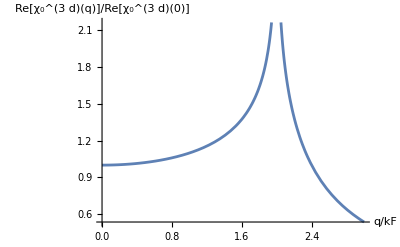

```mathematica
h:=1
Ω:=2Pi
m:=1
kF:=1
norm=Limit[int2[[1]],q->0]
Plot[{int[[1]],int2[[1]]}/norm/.q->q2,{q2,0,3*kF},AxesLabel->{"q/kF","Re[χ_0^(3  d)(q)]/Re[χ_0^(3  d)(0)]"}]
```

```mathematica
ClearAll["Global`*"]
X3d[k_]:=2Pi/Ω m/h^2 (1/(q^2+2q k)+1/(q^2-2q k))(kF^2-k^2)
int=Integrate[X3d[k],{k,-kF,kF},PrincipalValue->True]
int2=Integrate[X3d[k],{k,-kF,kF},PrincipalValue->False]
```

ConditionalExpression[(m π (2 kF q+(4 kF^2-q^2) ArcCoth[(2 kF)/q]))/(h^2 q Ω), q≠0&&kF≥0&&4 kF^2>q^2]

ConditionalExpression[(m π (2 kF q+(4 kF^2-q^2) ArcTanh[(2 kF)/q]))/(h^2 q Ω), ]

1/π

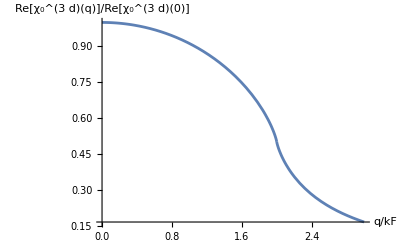

```mathematica
h:=1
Ω:=4Pi^2
m:=1
kF:=1
norm=Limit[int[[1]],q->0]
Plot[{int[[1]],int2[[1]]}/norm/.q->q2,{q2,0,3*kF},AxesLabel->{"q/kF","Re[χ_0^(3  d)(q)]/Re[χ_0^(3  d)(0)]"}]
```